# Lab 5 - Mathematica

## Problem 1 ________________________________________

ColorDataFunction[…]

plot[{f x,0,5 f}]

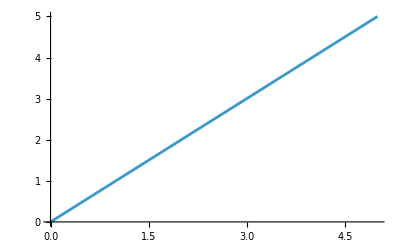

```mathematica
ColorData["Pastel"]
plot[f{x,0,5}]
Plot[y=x,{x,0,5}]
```

```mathematica
ColorDataFunction[…]
```

ColorDataFunction[…]

## Problem 2 ____________________________

```mathematica
f[t_]:=α*Log[a t]Cos[ω t]Sin[ω t]
f'[t]
f''[t]
```

α ω Cos[t ω]^2 Log[a t]+(α Cos[t ω] Sin[t ω])/t-α ω Log[a t] Sin[t ω]^2

(2 α ω Cos[t ω]^2)/t-(α Cos[t ω] Sin[t ω])/t^2-4 α ω^2 Cos[t ω] Log[a t] Sin[t ω]-(2 α ω Sin[t ω]^2)/t

## Problem 3 ____________________________

```mathematica
W[x_]:=F[x]G[x]H[x]
W'[x]
```

G[x] H[x] F'[x]+F[x] H[x] G'[x]+F[x] G[x] H'[x]

## Problem 4 ____________________________

```mathematica
g=9.81;
L= 10
ω0=SquareRoot[g/L];


s=NDSolve[{ϕ''[t]==-(ω0^2)*Sin[ϕ[t]],ϕ[0]==30*Degree,ϕ'[0]==0},ϕ,{t,0,2}];

Plot[Evaluate[ϕ[t]/. s],{t,0,2},AxesLabel->{"t (s)","ϕ (rad)"}]
```

10

NDSolve::dvnoarg: The function ϕ appears with no arguments.

ReplaceAll::reps: {NDSolve[{(-0.981 Sin ϕ)[t]==-Sin[ϕ[«1»]] SquareRoot[«1»]^2,ϕ[0]==30 °,ϕ'[0]==0},ϕ,{t,0,2}]} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

NDSolve::dsvar: 0.0000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{(-0.981 Sin ϕ)[0.0000408571]==-Sin[ϕ[«1»]] SquareRoot[«1»]^2,ϕ[0]==30 °,ϕ'[0]==0},ϕ,{0.0000408571,0,2}]} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

NDSolve::dsvar: 0.0000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{(-0.981 Sin ϕ)[0.0000408571]==-1. Sin[ϕ[«1»]] SquareRoot[«1»]^2,ϕ[0.]==0.523599,ϕ'[0.]==0.},ϕ,{0.0000408571,0.,2.}]} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0408572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

## Problem 5 ____________________________

```mathematica
Graphics3D[{Gray,Cylinder[{{0,0,2},{0,0,10}},0.05],Darker[Blue],Cylinder[{{0,0,0},{0,0,2}},3]},Boxed->False,ViewPoint->{2,-2,1}]
```

-Graphics3D-